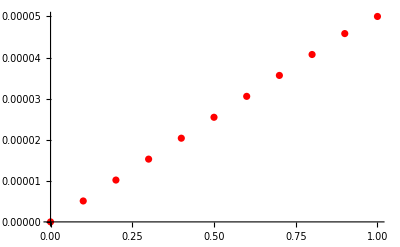

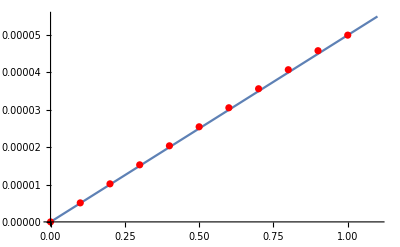

```mathematica
k=ReadList["C:\\Users\\vbole\\OneDrive\\Рабочий стол\\Study\\Kurs6\\out.txt", {Number, Number}];
boardCond = 0.00005;
p = 100000;
e =200000000000000;
exactSol[t_]:= 0.00005 * t; 
plot = ListPlot[k, PlotStyle->Red]
plot1 =Plot[exactSol[x],{x, 0,1.1}];
Show[plot1, plot]
```